# Code for Additional Figures

This file contains the code for figures included in the paper but not in Models 1 or 2 (Figs 1, 2, and A.1-4). If downloading files, updated the “saveto” location before running.

## Figure 1

Code for creating Fig 1. Note that this will not reproduce exactly the same figures between runs due to stochasticity. Subfigures were compiled in Adobe Illustrator 2024.

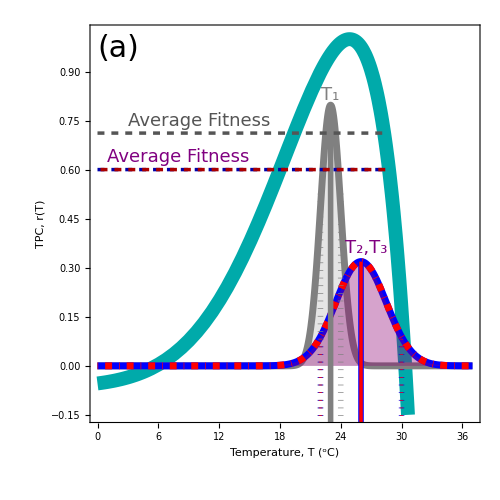

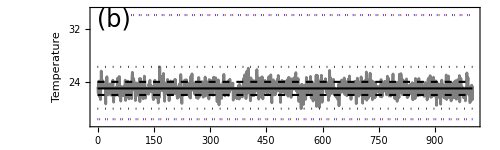

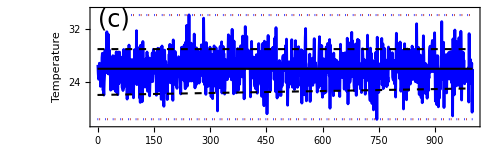

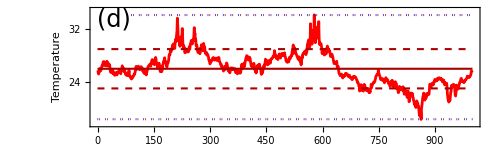

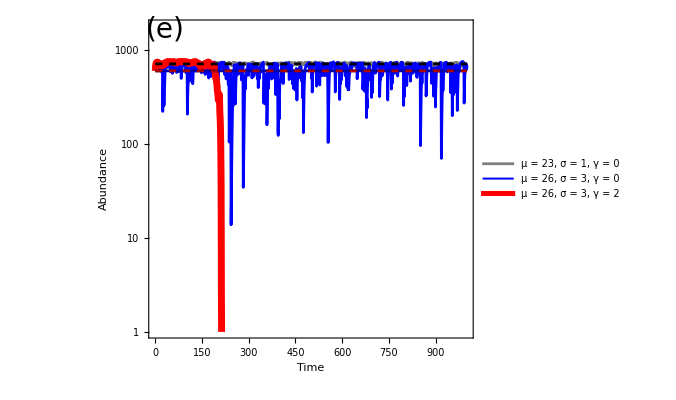

```mathematica
(*background functions for spectral synthesis and mimicry*)
cmplx[mod_,arg_]:=ExpToTrig[mod Exp[I arg]];

SpecSynFourier[γ_,Nobs_,μ_:0,σ_:1,seed_:0]:=Module[{
phase,f,vec},
If[seed==0,SeedRandom[],SeedRandom[seed]];
phase=RandomReal[{0,2Pi},Nobs];
f=Range[1/Nobs,1,1/Nobs];
vec=InverseFourier[Join[{0+0I},Table[cmplx[1/(f[[i]]^(γ/2)),phase[[i]]],{i,1,(Nobs-1)}]],FourierParameters->{-1,1}];
Standardize[Re[vec]]*σ+μ];

Mimic1[x_,z_]:=Module[{y},
y=x;
Do [y[[Ordering[z,i][[i]]]]=x[[i]],{i,1,Length[x]}];
y];

(*TPC functions*)
gain[T_]:=Exp[-((T-TI)^2)/β];
loss[T_]:=ma Exp[mb T]+mc;
r[T_]:=gain[T]-loss[T]; 

(*example TPC parameters*)
TI=29; 
β=180; 
ma=0.000005;
mb=0.4;
mc=0.05;

(*closed form solution of the r-alpha model*)
nt[t_,ntlast_]:=(r[Z[[t]]]Exp[r[Z[[t]]] ])/((r[Z[[t]]]/ntlast-α)+α Exp[r[Z[[t]]]]);

(*Subplot a: plot TPC against frequency distributions of temperatures*)
TPChist=Show[Plot[r[T]/.755,{T,0,37},PlotStyle->{Thickness[0.02],Darker[Cyan]},PlotRange->{{0,37},{-.15,1.02}},Frame->{True,True,False,True},FrameStyle->24,FrameLabel->{"Temperature, T (^oC)",Style["TPC, r(T)",Darker[Cyan]],None,Style["Temperature Distributions             ",Gray]},LabelStyle->Directive[Black],FrameTicks->{Automatic,{0,0.25,0.5,0.75,1},None,Automatic},ImageSize->500,AspectRatio->1,
Epilog->{Text[Style["(a)",Black,30],{2,.97}],
Text[Style["Average Fitness",Darker[Gray],18],{10,.75}],
Text[Style["Average Fitness",Purple,18],{8,.64}],
Text[Style["T_1",Gray,18],{23,.83}],
Text[Style["T_2,T_3",Purple,18],{26.5,.36}],

Thickness[0.008],Gray,Line[{{23,-0.2},{23,.797}}],
Blue,Line[{{26,-0.2},{26,.319}}],
Red,Thickness[0.005],Line[{{26,-0.2},{26,.319}}],

Thickness[0.008],Dotted,Gray,Line[{{23+1,-0.2},{23+1,.527}}],Line[{{23-1,-0.2},{23-1,.527}}],
Blue,Line[{{26+4,-0.2},{26+4,.088}}],Line[{{26-4,-0.2},{26-4,.088}}],
Red,Thickness[0.005],Line[{{26+4,-0.2},{26+4,.088}}],Line[{{26-4,-0.2},{26-4,.088}}],

Dashed,Darker[Gray],{Dashed,Darker[Red]},Line[{{0,.7125},{28.3,.7125}}],
Darker[Blue],Line[{{0,.6008},{28.4,.6008}}],
Darker[Red],Line[{{0.3,.6008},{28.4,.6008}}]}],
Plot[2*PDF[NormalDistribution[23,1],x],{x,0,37},PlotStyle->{Thickness[0.01],Gray},PlotRange->Full,Filling->Axis, Frame->{True,False,False,True},FrameLabel->{None,None,None,"Frequency"},LabelStyle->Directive[Black],ImageSize->500],
Plot[2*PDF[NormalDistribution[26,2.5],x],{x,0,37},PlotStyle->{Thickness[0.01],Blue},Filling->Axis,PlotRange->{{0,37},Automatic(*{0,320}*)}, Frame->{True,False,False,True},FrameLabel->{None,None,None,"Frequency"},LabelStyle->Directive[Black],ImageSize->500],
Plot[2*PDF[NormalDistribution[26,2.5],x],{x,0,37},PlotStyle->{Thickness[0.01],DotDashed,Red},Filling->Axis,PlotRange->{{0,37},Automatic(*{0,320}*)}, Frame->{True,False,False,True},FrameLabel->{None,None,None,"Frequency"},LabelStyle->Directive[Black],ImageSize->500]]

(*subplots b, c, d, e: plot time series of temperatures and abundances for 3 time series*)
α=.001; (*density dependence parameter*)
tmax=1000; (*number of time steps*)
maxsims=1;(*number of replicates*)
γvals=Range[0,2,2];  (*Autocorrelation level: 0, 2*)
μTvals=Range[23,26,3]; (*Mean temp: 23, 26*)
σTvals=Range[1,2.5,1.5]; (*St dev of temp: 1, 2.5*)

(*create temperature time series*)
W=ConstantArray[0,{Length[μTvals],Length[σTvals],tmax}];
Do[W[[i,j,k]]=InverseCDF[NormalDistribution[μTvals[[i]],σTvals[[j]]],k*(1/tmax)],{i,1,Length[μTvals]},{j,1,Length[σTvals]},{k,1,tmax-1}]
Do[W[[i,j,tmax]]=InverseCDF[NormalDistribution[μTvals[[i]],σTvals[[j]]],(tmax-.5)*(1/tmax)],{i,1,Length[μTvals]},{j,1,Length[σTvals]}];

(*calculate initial population sizes (=the avg predicted by the distribution)*)
ninit=ConstantArray[0,{Length[μTvals],Length[σTvals]}];
Do[ninit[[i,k]]=(Mean[Table[r[W[[i,k,j]]],{j,1,tmax}]])/α,{k,1,Length[σTvals]},{i,1,Length[μTvals]}]
lt23=ConstantArray[ninit[[1,1]],tmax];
lt26=ConstantArray[ninit[[2,2]],tmax];

(*initialize array to store extinction times; =tmax if not extinct*)
extTime=ConstantArray[tmax,{Length[γvals],Length[μTvals],Length[σTvals],maxsims}];
(*initialize array to store population sizes*)
p1=ConstantArray[0,{Length[γvals],Length[μTvals],Length[σTvals],maxsims,tmax}];
Do[p1[[i,j,m,l,1]]=ninit[[j,m]],{l,1,maxsims},{m,1,Length[σTvals]},{j,1,Length[μTvals]},{i,1,Length[γvals]}]

(*create array to store temperature time series*)
temps1=ConstantArray[0,{Length[μTvals],Length[σTvals],Length[γvals]}];

(*run simulation*)
SetSharedVariable[p1,extTime];
Do[γ=γvals[[i]];
μT=μTvals[[j]];
σT=σTvals[[m]];

X=SpecSynFourier[γ,tmax];
Z=Mimic1[W[[j,m]],X];
envt=Interpolation[Z,InterpolationOrder->0];

temps1[[i,j,m]]=Z;

Do[p1[[i,j,m,l,k]]=nt[k,p1[[i,j,m,l,k-1]]];
If[p1[[i,j,m,l,k]]<1,extTime[[i,j,m,l]]=k;
Break[]];,{k,2,tmax}],

{l,1,maxsims},{m,1,Length[σTvals]},{j,1,Length[μTvals]},{i,1,Length[γvals]}]

(*generate subfigures*)
framesize=20;
sublabel=24;

series1=ListLinePlot[{temps1[[1,1,1]]},PlotStyle->{Gray,Blue,Red},PlotRange->{{0,tmax},{17.5,35}},Frame->{True,True,False,False},FrameStyle->framesize,FrameLabel->{"Time","Temperature"},LabelStyle->Directive[Black],ImageSize->500,AspectRatio->.3,
Epilog->{{Text[Style["(b)",Black,sublabel],{45,33.5}]},
Thickness[0.003],Black,Line[{{0,23},{tmax,23}}],
Dashed,Line[{{0,23+1},{tmax,23+1}}],Line[{{0,23-1},{tmax,23-1}}],
Dotted,Black,Line[{{0,26.29},{tmax,26.29}}],Line[{{0,19.91},{tmax,19.91}}],
Dotted,Blue,Line[{{90,34.2},{tmax,34.2}}],Line[{{0,18.3},{tmax,18.3}}],
Dotted,Darker[Red],Line[{{95,34.2},{tmax,34.2}}],Line[{{5,18.3},{tmax,18.3}}]}]
series2=ListLinePlot[{temps1[[1,2,2]]},PlotStyle->{Blue},PlotRange->{{0,tmax},{17.5,35}},Frame->{True,True,False,False},FrameStyle->framesize,FrameLabel->{"Time","Temperature"},LabelStyle->Directive[Black],ImageSize->500,AspectRatio->.3,
Epilog->{{Text[Style["(c)",Black,sublabel],{45,33.5}]},
Thickness[0.003],Black,Line[{{0,26},{tmax,26}}],
Dashed,Line[{{0,26+3},{tmax,26+3}}],Line[{{0,26-4},{tmax,26-3}}],
Dotted,Blue,Line[{{90,34.2},{tmax,34.2}}],Line[{{0,18.3},{tmax,18.3}}],
Dotted,Darker[Red],Line[{{95,34.2},{tmax,34.2}}],Line[{{5,18.3},{tmax,18.3}}]}]
series3=ListLinePlot[{temps1[[2,2,2]]},PlotStyle->{Red},PlotRange->{{0,tmax},{17.5,35}},Frame->{True,True,False,False},FrameStyle->framesize,FrameLabel->{"Time","Temperature"},LabelStyle->Directive[Black],ImageSize->500,AspectRatio->.3,
Epilog->{{Text[Style["(d)",Black,sublabel],{45,33.5}]},
Thickness[0.003],Darker[Red],Line[{{0,26},{tmax,26}}],
Dashed,Line[{{0,26+3},{tmax,26+3}}],Line[{{0,26-3},{tmax,26-3}}],
Dotted,Blue,Line[{{90,34.2},{tmax,34.2}}],Line[{{0,18.3},{tmax,18.3}}],
Dotted,Darker[Red],Line[{{95,34.2},{tmax,34.2}}],Line[{{5,18.3},{tmax,18.3}}]}]

data={p1[[1,1,1,1]],p1[[1,2,2,1]],p1[[2,2,2,1]],lt23,lt26,lt26};
abundances=ListLinePlot[data,ScalingFunctions->{"Linear","Log"},PlotStyle->{Gray,{Thickness[0.004],Blue},{Thickness[0.01],Red},{Dashed,Black},Darker[Blue],{Dashed,Darker[Red]}},PlotLegends->Placed[{"μ = 23, σ = 1, γ = 0","μ = 26, σ = 3, γ = 0","μ = 26, σ = 3, γ = 2"},{0.8,0.2}],PlotRange->{{0,tmax},{1,1800}},Frame->{True,True,False,False},FrameStyle->16,FrameLabel->{"Time","Abundance"},LabelStyle->Directive[Black],ImageSize->500,AspectRatio->.8,Epilog->{Text[Style["(e)",Black,28],Scaled[{0.05,0.97}]]}]

(*saveto="/EXPORTLOCATION/";
Export[saveto<>"tpcHist.pdf",TPChist,ImageResolution->1000];
Export[saveto<>"series1.pdf",series1,ImageResolution->1000];
Export[saveto<>"series2.pdf",series2,ImageResolution->1000];
Export[saveto<>"series3.pdf",series3,ImageResolution->1000];
Export[saveto<>"abundances.pdf",abundances,ImageResolution->1000];*)
```

## Figure 2

This code creates a figure of the generic TPCs used in the initial models and the corresponding thermal distributions (Fig 2).

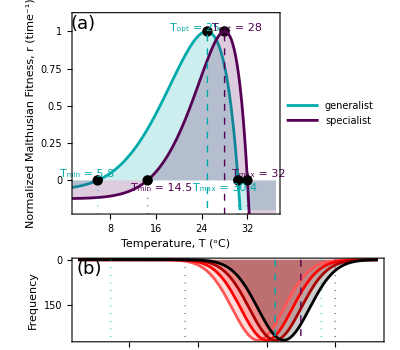

```mathematica
(* Parameters of the TPC model (generalist, then specialist)*)
TI=29; (*move bopt*)
β=180; (*make narrower*)
ma=0.000005;
mb=0.4;
mc=0.05;
TI1=35;
β1=170;

gencol=Darker[Cyan];
specol=Darker[Purple];

gopt=25;
sopt=28;
gmin=5.8;
smin=14.54;
gmax=30.4;
smax=32;

(* Plot*)
TPCs=Show[Plot[r[T]/.755,{T,0,37},Filling->Axis,PlotStyle->gencol,PlotLegends->Placed[{"generalist"},{0.185,0.8}],PlotRange->{{2,37},{-.2,1.1}},Frame->{True,True,False,False},FrameStyle->14,FrameLabel->{"Temperature, T (^oC)","Normalized Malthusian Fitness, r (time^-1)"},LabelStyle->Directive[Black],FrameTicks->{Automatic,{0,0.25,0.5,0.75,1}},ImageSize->500],
Plot[(r[T-2,TI1,β1,ma,mb,mc])/.4067,{T,0,37},Filling->Axis,PlotStyle->specol,PlotLegends->Placed[{"specialist"},{0.182,0.7}]],
Epilog->{Text[Style["(a)",Black,18],{3.3,1.05}],
{Text[Style["T_opt = 25",gencol],{22.8,1.02}]},{Text[Style["T_min = 5.8",gencol],{4,.04}]},{Text[Style["T_max = 30.4",gencol],{28,-.05}]},{Text[Style["T_opt = 28",specol],{30.2,1.02}]},
{Text[Style["T_min = 14.5",specol],{17,-.05}]},{Text[Style["T_max = 32",specol],{34,.04}]},
{Black,PointSize[0.015],Point[{gmin,0}]},
{Black,PointSize[0.015],Point[{smin,0}]},{Black,PointSize[0.015],Point[{gopt,1}]},
{Black,PointSize[0.015],Point[{sopt,1}]},
{Black,PointSize[0.015],Point[{gmax,0}]},{Black,PointSize[0.015],Point[{smax,0}]},
Thick,specol,Dotted,Line[{{smax,-0.015},{smax,-.25}}],Line[{{smin,-0.015},{smin,-.25}}],Dashed,Line[{{sopt,.98},{sopt,-.02}}],Line[{{sopt,-.09},{sopt,-.25}}],
gencol,Dotted,Line[{{gmax,-0.015},{gmax,-.25}}],Line[{{gmin,-0.015},{gmin,-.25}}],Dashed,Line[{{gopt,.98},{gopt,-.25}}]}];

ymax=285;
dists=Plot[Table[PDF[NormalDistribution[μ,σ],x]*2000,{μ,{23,24,25,26}},{σ,{3}}]//Evaluate,{x,2,37},Filling->Axis,PlotRange->{{1.7,37},{0,ymax}},PlotStyle->{Lighter[Red],Red,Darker[Red],Black},ScalingFunctions->{Automatic,"Reverse"},
PlotLegends->Placed[{"μ = 23","μ = 24","μ = 25","μ = 26"},{Scaled[{0.15,0.5}],{0,0.5}}],
Frame->{False,True,True,False},FrameStyle->14,FrameLabel->{None,"Frequency",None,None},LabelStyle->Directive[Black],ImageSize->500,AspectRatio->1/4,
Epilog->{Text[Style["(b)",Black,18],{3.3,-30}],
Thick,specol,Dotted,Line[{{32,0},{32,-ymax}}],Line[{{14.5,0},{14.5,-ymax}}],Dashed,Line[{{28,0},{28,-ymax}}],
gencol,Dotted,Line[{{30.4,0},{30.4,-ymax}}],Line[{{5.8,0},{5.8,-ymax}}],Dashed,Line[{{25,0},{25,-ymax}}]}];

TPCfig=GraphicsColumn[{TPCs,dists},Spacings->0]
(*Export[saveto<>"Figure2.eps",TPCfig,ImageResolution->1000]*)
```

## Appendix S2 Figure S1

This recreates the Gaussian-quadratic TPC of the organisms most similar to those used in initial models.

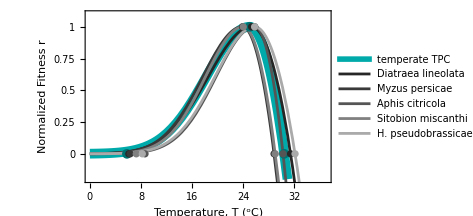
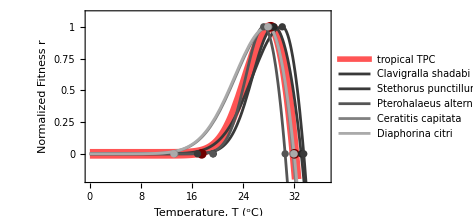

/Users/alisonrobey/Documents/PhD Year 3 (2023-2024)/Ch1/Code/TPCsComparison_Deutschfit.eps

```mathematica
rD[T_,Topt_,σp_,CTmax_]:=If[T≤Topt,Exp[-((T-Topt)/(2σp))^2],1-((T-Topt)/(Topt-CTmax))^2]; 

(*temporate TPCs*)
CTmax=31.4;Topt=25.3;σp=4.8;
CTmax2=28.82;Topt2=23.88;σp2=4.395;
CTmax3=30.225;Topt3=25.8;σp3=4.29375;
CTmax4=29;Topt4=24;σp4=4.185;
CTmax5=32.1;Topt5=25.78;σp5=4.395;

(*tropical TPCs*)
TCTmax=33.0677;TTopt=28.8;Tσp=2.375;
TCTmax2=33.46;TTopt2=30.1;Tσp2=3.315;
TCTmax3=30.55;TTopt3=27.2;Tσp3=1.9875;
TCTmax4=31.78;TTopt4=27.98;Tσp4=3.675;
TCTmax5=31.96;TTopt5=27.84;Tσp5=3.675;

DeutschTPCs=Show[Plot[rD[T,25,4.8,30.4],{T,0,37},PlotStyle->{Darker[Cyan],Thickness[0.02]},PlotLegends->Placed[{"temperate TPC"},{0.22,0.8}],PlotRange->{{0,37},{-.2,1.1}},Frame->{True,True,False,False},FrameStyle->14,FrameLabel->{"Temperature, T (^oC)","Normalized Fitness r"},LabelStyle->Directive[Black],FrameTicks->{Automatic,{0,0.25,0.5,0.75,1}},ImageSize->500,PlotRange->{-0.2,1.1}],
Plot[rD[T,Topt,σp,CTmax],{T,0,37},PlotLegends->Placed[{"Diatraea lineolata"},{0.22,0.75}],PlotStyle->Darker[Darker[Darker[Gray]]]],
Plot[rD[T,Topt2,σp2,CTmax2],{T,0,37},PlotLegends->Placed[{"Myzus persicae"},{0.22,0.7}],PlotStyle->Darker[Darker[Gray]]],
Plot[rD[T,Topt3,σp3,CTmax3],{T,0,37},PlotLegends->Placed[{"Aphis citricola"},{0.22,0.65}],PlotStyle->Darker[Gray]],
Plot[rD[T,Topt4,σp4,CTmax4],{T,0,37},PlotLegends->Placed[{"Sitobion miscanthi"},{0.22,0.6}],PlotStyle->Gray],
Plot[rD[T,Topt5,σp5,CTmax5],{T,0,37},PlotLegends->Placed[{"H. pseudobrassicae"},{0.22,0.55}],PlotStyle->Lighter[Gray]],

Epilog->{{Darker[Darker[Cyan]],PointSize[0.02],Point[{30.4,0}]},
{Darker[Darker[Cyan]],PointSize[0.02],Point[{25,1}]},{Darker[Darker[Cyan]],PointSize[0.02],Point[{5.8,0}]},

{Darker[Darker[Darker[Gray]]],PointSize[0.015],Point[{CTmax,0}]},
{Darker[Darker[Darker[Gray]]],PointSize[0.015],Point[{Topt,1}]},{Darker[Darker[Darker[Gray]]],PointSize[0.015],Point[{6.1,0}]},

{Darker[Darker[Gray]],PointSize[0.015],Point[{CTmax2,0}]},
{Darker[Darker[Gray]],PointSize[0.015],Point[{Topt2,1}]},{Darker[Darker[Gray]],PointSize[0.015],Point[{6.3,0}]},

{Darker[Gray],PointSize[0.015],Point[{CTmax3,0}]},
{Darker[Gray],PointSize[0.015],Point[{Topt3,1}]},{Darker[Gray],PointSize[0.015],Point[{8.625,0}]},

{Gray,PointSize[0.015],Point[{CTmax4,0}]},
{Gray,PointSize[0.015],Point[{Topt4,1}]},{Gray,PointSize[0.015],Point[{7.26,0}]},

{Lighter[Gray],PointSize[0.015],Point[{CTmax5,0}]},
{Lighter[Gray],PointSize[0.015],Point[{Topt5,1}]},{Lighter[Gray],PointSize[0.015],Point[{8.2,0}]}},
ImageSize->350];

DeutschTPCsTrop=Show[Plot[rD[T,28.3,2.7,32],{T,0,37},PlotStyle->{Lighter[Red],Thickness[0.02]},PlotLegends->Placed[{"tropical TPC"},{0.3,0.8}],PlotRange->{{0,37},{-.2,1.1}},Frame->{True,True,False,False},FrameStyle->14,FrameLabel->{"Temperature, T (^oC)","Normalized Fitness r"},LabelStyle->Directive[Black],FrameTicks->{Automatic,{0,0.25,0.5,0.75,1}},ImageSize->500,PlotRange->{-0.2,1.1}],
Plot[rD[T,TTopt,Tσp,TCTmax],{T,0,37},PlotLegends->Placed[{"Clavigralla shadabi"},{0.3,0.75}],PlotStyle->Darker[Darker[Gray]]],
Plot[rD[T,TTopt2,Tσp2,TCTmax2],{T,0,37},PlotLegends->Placed[{"Stethorus punctillum"},{0.3,0.7}],PlotStyle->Darker[Darker[Gray]]],
Plot[rD[T,TTopt3,Tσp3,TCTmax3],{T,0,37},PlotLegends->Placed[{"Pterohalaeus alternatus"},{0.3,0.65}],PlotStyle->Darker[Gray]],
Plot[rD[T,TTopt4,Tσp4,TCTmax4],{T,0,37},PlotLegends->Placed[{"Ceratitis capitata"},{0.3,0.6}],PlotStyle->Gray],
Plot[rD[T,TTopt5,Tσp5,TCTmax5],{T,0,37},PlotLegends->Placed[{"Diaphorina citri"},{0.3,0.55}],PlotStyle->Lighter[Gray]],

Epilog->{{Darker[Darker[Red]],PointSize[0.02],Point[{32,0}]},
{Darker[Darker[Red]],PointSize[0.02],Point[{28.3,1}]},{Darker[Darker[Red]],PointSize[0.02],Point[{17.5,0}]},

{Darker[Darker[Darker[Gray]]],PointSize[0.015],Point[{TCTmax,0}]},
{Darker[Darker[Darker[Gray]]],PointSize[0.015],Point[{TTopt,1}]},{Darker[Darker[Darker[Gray]]],PointSize[0.015],Point[{19.3,0}]},

{Darker[Darker[Gray]],PointSize[0.015],Point[{TCTmax2,0}]},
{Darker[Darker[Gray]],PointSize[0.015],Point[{TTopt2,1}]},{Darker[Darker[Gray]],PointSize[0.015],Point[{16.84,0}]},

{Darker[Gray],PointSize[0.015],Point[{TCTmax3,0}]},
{Darker[Gray],PointSize[0.015],Point[{TTopt3,1}]},{Darker[Gray],PointSize[0.015],Point[{19.25,0}]},

{Gray,PointSize[0.015],Point[{TCTmax4,0}]},
{Gray,PointSize[0.015],Point[{TTopt4,1}]},{Gray,PointSize[0.015],Point[{13.28,0}]},

{Lighter[Gray],PointSize[0.015],Point[{TCTmax5,0}]},
{Lighter[Gray],PointSize[0.015],Point[{TTopt5,1}]},{Lighter[Gray],PointSize[0.015],Point[{13.14,0}]}},
ImageSize->350];

stackedTPCs=Row[{DeutschTPCs,DeutschTPCsTrop}]

Export[saveto<>"TPCsComparison_Deutschfit.pdf",stackedTPCs,ImageResolution->1000]
```

## Appendix S4 Figures S1 & S2

This code tests the impact of the timestep size, δt, on population dynamics. Models are stochastic, so will not output exactly the same graphs on every run.

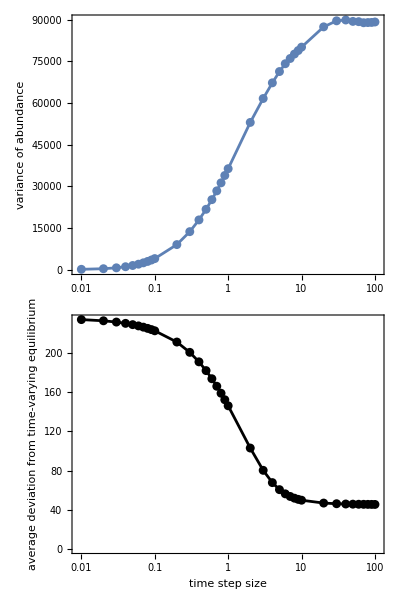

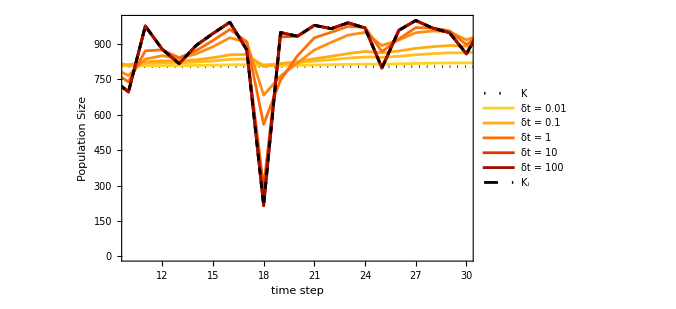

```mathematica
(*background functions - same as other versions with δt added in and an edit to the indexing in Z to allow for multiple runs*)
r[T_,Topt_,σp_,CTmax_]:=If[T≤Topt,Exp[-((T-Topt)/(2σp))^2],1-((T-Topt)/(Topt-CTmax))^2]; 

nt[t_,ntlast_,δt_,i_]:=(r[Z[[i,t]],Topt,σp,CTmax]*Exp[r[Z[[i,t]],Topt,σp,CTmax]*δt ])/((r[Z[[i,t]],Topt,σp,CTmax]/ntlast-α)+α Exp[r[Z[[i,t]],Topt,σp,CTmax]*δt]);

(*unchanging parameters for TPC and temps*)
Topt=25;σp=5;CTmax=30; (*TPC params*)
α=.001;
μT=25; σT=3; (*temp params-values for some extinction risk*)

tmax=100; (*number of time steps*)
nmax=500; (*number of replicates*)

(*initializing*)
δts=Join[Range[0.01,0.09,0.01],Range[0.1,0.9,0.1],Range[1,10],Range[20,100,10]];

means=vars=stdevs=ConstantArray[0,{nmax,Length[δts]}];
cvs=equidists=ConstantArray[0,Length[δts]];
extTime=ConstantArray[tmax,{nmax,Length[δts]}];

(*set up thermal regimes*)
Z=ConstantArray[0,{nmax,tmax}];
Do[Z[[i,k]]=RandomVariate[NormalDistribution[μT,σT]],
{k,1,tmax},{i,1,nmax}];

μr=ConstantArray[0,nmax];
Do[μr[[i]]=Mean[Table[r[Z[[i,k]],Topt,σp,CTmax],{k,1,tmax}]],{i,1,nmax}];

ninit=ConstantArray[0,nmax];
Do[ninit[[i]]=μr[[i]]/α,{i,1,nmax}];

Ks=ConstantArray[0,{nmax,tmax}];
Do[Ks[[i,k]]=r[Z[[i,k]],Topt,σp,CTmax]/α,{k,1,tmax},{i,1,nmax}];

p=ConstantArray[0,{nmax,Length[δts],tmax}];
Do[p[[i,All,1]]=ninit[[i]],{i,1,nmax}];

(*simulations*)
Do[p[[i,j,k]]=nt[k,p[[i,j,k-1]],δts[[j]],i];
If[p[[i,j,k]]<((1/α)*10^-6),extTime[[i,j]]=k(*;Break[]*)],
{k,2,tmax},{j,1,Length[δts]},{i,1,nmax}]

(*calculate stats*)
Do[If[extTime[[i,j]]==tmax,

means[[i,j]]=Mean[p[[i,j]]];
vars[[i,j]]=Variance[p[[i,j]]];
stdevs[[i,j]]=StandardDeviation[p[[i,j]]],

means[[i,j]]=Mean[Take[p[[i,j]],extTime[[i,j]]]];
vars[[i,j]]=Variance[Take[p[[i,j]],extTime[[i,j]]]];
stdevs[[i,j]]=StandardDeviation[Take[p[[i,j]],extTime[[i,j]]]];

],{j,1,Length[δts]},{i,1,nmax}]

allmeans=Mean[means];allvars=Mean[vars];allstdevs=Mean[stdevs];
meanplot=Transpose[{δts,allmeans}];varplot=Transpose[{δts,allvars}];stdevplot=Transpose[{δts,allstdevs}];

ListLogLinearPlot[meanplot,PlotLabel->"Means"];
ListLogLinearPlot[varplot,PlotLabel->"Vars"];
ListLogLinearPlot[stdevplot,PlotLabel->"Stdevs"];

Do[cvs[[j]]=allstdevs[[j]]/allmeans[[j]],
{j,1,Length[δts]}];
cvplot=Transpose[{δts,cvs}];
ListLogLinearPlot[cvplot,PlotLabel->"CVs"];

dist=ConstantArray[0,{nmax,Length[δts],tmax}];
Do[dist[[i,j,k]]=Abs[Ks[[i,k]]-p[[i,j,k]]],{k,1,tmax},{j,1, Length[δts]},{i,1,nmax}];
meandist=ConstantArray[0,{nmax,Length[δts]}];
Do[meandist[[i,j]]=Mean[dist[[i,j]]],{j,1, Length[δts]},{i,1,nmax}];
meandists=Mean[meandist];
meandistplot=Transpose[{δts,meandists}];
ListLogLinearPlot[meandistplot,PlotLabel->"MeanDists"];

timestepplot=Column[{
Show[ListLogLinearPlot[varplot,Joined->True,PlotRange->{{0.009,110},Automatic},GridLines->{δts,None},
Frame->{True,True,False,False},FrameStyle->14,FrameLabel->{None,"variance of abundance"},AspectRatio->.4,ImageSize->500],ListLogLinearPlot[varplot]],
Show[ListLogLinearPlot[meandistplot,PlotStyle->Black,Joined->True,PlotRange->{{0.009,110},Automatic},GridLines->{δts,None},
Frame->{True,True,False,False},FrameStyle->14,FrameLabel->{"time step size","average deviation from \n time-varying equilibrium"},AspectRatio->.4,ImageSize->500],ListLogLinearPlot[meandistplot,PlotStyle->Black]]},Spacings->{0,0}]

colorFunc=ColorData["SolarColors"];
run=15;
total=9;
line=ConstantArray[ninit[[run]],tmax];
timestepseriesplot=Show[
ListLinePlot[line,PlotRange->{{10,30},{0,1000}},PlotStyle->{Black,Dotted},PlotLegends->{"K"},Frame->{True,True,False,False},FrameStyle->14,FrameLabel->{"time step","Population Size"}],
ListLinePlot[p[[run,1]],PlotStyle->colorFunc[9/total],PlotLegends->{"δt = 0.01"}],
ListLinePlot[p[[run,5]],PlotStyle->colorFunc[8/total](*,PlotLegends->{"δt = 0.05"}*)],
ListLinePlot[p[[run,10]],PlotStyle->colorFunc[7/total],PlotLegends->{"δt = 0.1"}],
ListLinePlot[p[[run,14]],PlotStyle->colorFunc[6/total](*,PlotLegends->{"δt = 0.5"}*)],
ListLinePlot[p[[run,19]],PlotStyle->colorFunc[5/total],PlotLegends->{"δt = 1"}],
ListLinePlot[p[[run,23]],PlotStyle->colorFunc[4/total](*,PlotLegends->{"δt = 5"}*)],
ListLinePlot[p[[run,28]],PlotStyle->colorFunc[3/total],PlotLegends->{"δt = 10"}],
ListLinePlot[p[[run,32]],PlotStyle->colorFunc[2/total](*,PlotLegends->{"δt = 50"}*)],
ListLinePlot[p[[run,37]],PlotStyle->colorFunc[1/total],PlotLegends->{"δt = 100"}],
ListLinePlot[Ks[[run]],PlotStyle->{Black,Dashed},PlotLegends->{Subscript["K","i"]}],
ImageSize->500]

Export[saveto<>"timestepplot.pdf",timestepseriesplot,ImageResolution->1000]
Export[saveto<>"timestepseriesplot.pdf",timestepplot,ImageResolution->1000]
```